VAJA2

```mathematica
izraz=(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)
ReplaceAll[izraz, x->1]
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

-3

```mathematica
-3
ReplaceAll[izraz, x->2]
```

34/27

```mathematica
ReplaceAll[izraz, x ->3]
```

119/118

```mathematica
ReplaceAll[izraz,x->0]
```

-4

```mathematica
ReplaceAll[izraz, x->4]
```

```mathematica
144/145
ReplaceAll[izraz, x->5]
```

144/145

1547/1557

```mathematica
ReplaceAll[izraz,x->{1,2,3,4,5}]
```

#### {-3,34/27,119/118,144/145,1547/1557}

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

```mathematica
Table[izraz,1,10]
```

{{(4+3 x-2 x^2+x^5)/(-1-2 x+x^5),(4+3 x-2 x^2+x^5)/(-1-2 x+x^5),(4+3 x-2 x^2+x^5)/(-1-2 x+x^5),(4+3 x-2 x^2+x^5)/(-1-2 x+x^5),(4+3 x-2 x^2+x^5)/(-1-2 x+x^5),(4+3 x-2 x^2+x^5)/(-1-2 x+x^5),(4+3 x-2 x^2+x^5)/(-1-2 x+x^5),(4+3 x-2 x^2+x^5)/(-1-2 x+x^5),(4+3 x-2 x^2+x^5)/(-1-2 x+x^5),(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)}}

### 2.

```mathematica
sez ={10,20,30,40,50,60,70}
Take [sez, -2]
```

{10,20,30,40,50,60,70}

{60,70}

```mathematica
Take[sez, -2]
```

{60,70}

```mathematica
Part[sez, {2, 3, 5}]
```

{20,30,50}

```mathematica
Drop [sez {2, 4}]
```

Thread::tdlen: Objects of unequal length in {10,20,30,40,50,60,70} {2,4} cannot be combined.

{2,4} {10,20,30,40,50,60,70}

```mathematica
ClearAll[x,a, sez]
```

```mathematica
3.
```

```mathematica
sez = {x^6, x^2, a}
```

{x^6,x^2,a}

```mathematica
sez /. x ->3
```

{729,9,a}

```mathematica
sez/.x->x^2
```

{x^12,x^4,a}

```mathematica
sez/.x^2->x
```

{x^6,x,a}

```mathematica
sez/.x->{1,2,3}
```

{{1,64,729},{1,4,9},a}

```mathematica
sez/.{x->3,a->x}
```

{729,9,x}

```mathematica
ReplaceAll[sez,{x->3,a-> x}]
ReplaceRepeated [sez,{x->3,a-> x}]
```

{729,9,x}

{729,9,3}

```mathematica
sez//.{x->3,a-> x}
```

{729,9,3}

```mathematica
Table [ sez/.x->i,{i, 1, 3}]
```

{{1,1,a},{64,4,a},{729,9,a}}

```mathematica
4.Izračunaj odvode funkcij simbolično ter v navedenih točkah
```

```mathematica
D[x^5+4x^3-9,x] /.{{x->1},{x->2}}
```

{17,128}

```mathematica
ClearAll[f]
```

```mathematica
Map [f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
f[i_]: sez/.x->i
```

Syntax::sntxb: Expression cannot begin with "f[i_]:sez/.x→i".

```mathematica
D[E^(x^(1/4)),x]/.{{x->1}, {x->2}}
```

{ⅇ/4,(ⅇ^(2^(1/4)))/(4 2^(3/4))}

```mathematica
FullSimplify[D[ Abs[(x+1)],x],Element[x,Reals]&&x≠0]
```

Sign[1+x]

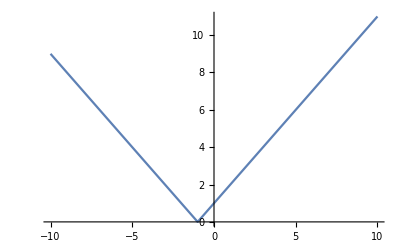

```mathematica
Plot[Abs[x+1],{x,-10,10}]
```

```mathematica
ClearAll[a,b,x]
```

```mathematica
D[g[x]=a x^2 + 3b,x]
```

2 a x

```mathematica
D[g[x]=a x^2 + 3b,x]/.{{x->1},{x->2}}
```

{2 a,4 a}

```mathematica
Naloga 5
```

```mathematica
ClearAll[f,g,h,a,x]
```

```mathematica
f[x_] := x^3 Log[4x+5]
```

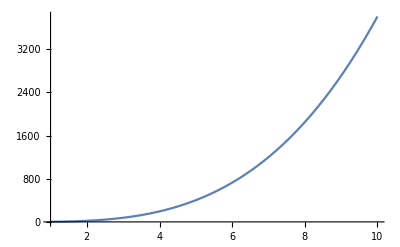

```mathematica
Plot[f[x],{x,1,10}]
```

```mathematica
x0=5
```

5

```mathematica
f[x0]//N
```

402.359

```mathematica
k = D[f[x],x]/. x->x0
```

20+75 Log[25]

```mathematica
k//N
```

```mathematica
261.41568686511505
ClearAll[x,y,n]
```

261.416

```mathematica
n/.Solve[y==kx +n/.{x->x0, y->f[x0]},n]//
First
```

```mathematica
-kx+125 Log[25]
ClearAll[f,x]
```

-kx+125 Log[25]

```mathematica
f[x]=5x^3-3x^2
```

```mathematica
g[x]=Log[3x]+2
```

2+Log[3 x]

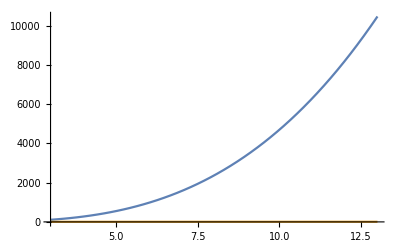

```mathematica
Plot[{f[x],{g[x]}},{x,3,13}]
```

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
narisi[f_,x0_,x_, zac_, kon_] :=Module[{k, enacba, enacba2, resitev, pravilo},k=D[f[x],x]/.{x->x0, y ->f[x0]};
resitev = Solve[enacba2, n];
pravilo = First[resitev];
n0 = n/. pravilo;
```

```mathematica
Plot[{f[x]...
```